## The snapshots needed for stress-fluctuation

```mathematica
Tlist1024={0.002,0.0025,0.0031,0.01, 0.01584893, 0.02511886 ,0.03981072, 0.06309573};
```

```mathematica
Tstring1024=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist1024
```

{0.00200000,0.00250000,0.00310000,0.01000000,0.01584893,0.02511886,0.03981072,0.06309573}

```mathematica
Tlist4096={0.002,0.0025,0.0031};
```

```mathematica
Tstring4096=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist4096
```

{0.00200000,0.00250000,0.00310000}

```mathematica
testdata=Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/nvt_N1024_p3.800_T",Tstring1024[[1]],"_0.nc"],"Data"];
```

```mathematica
timeNVT=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}];
```

```mathematica
stresses1024=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/stressNVT_N1024_p3.800_T",Tstring1024[[i]],"_0.csv"],"CSV"][[1]]*area,{i,Length[Tstring1024]}];
```

```mathematica
insGs1024=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/insGNVT_N1024_p3.800_T",Tstring1024[[i]],"_0.csv"],"CSV"][[1]],{i,Length[Tstring1024]}];
```

```mathematica
stresses4096=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N4096/stressNVT_N4096_p3.800_T",Tstring1024[[i]],"_0.csv"],"CSV"][[1]]*4096,{i,Length[Tstring4096]}];
```

```mathematica
insGs4096=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N4096/insGNVT_N4096_p3.800_T",Tstring1024[[i]],"_0.csv"],"CSV"][[1]],{i,Length[Tstring4096]}];
```

```mathematica
sisf=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/nvt_SISF_N1024_p3.800_T",Tstring1024[[i]],"_0.csv"],"CSV"][[1]],{i,Length[Tstring1024]}];
```

```mathematica
Dimensions[stresses1024]
```

{5,50000}

```mathematica
data=Import["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/nvt_N1024_p3.800_T0.00200000_0.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[…],/postion→NumericArray[…],/time→NumericArray[…],/type→NumericArray[…],/velocity→NumericArray[…]|>

```mathematica
G1Steps=Table[Table[1/area Mean[insGs1024[[i]][[1;;N]]],{N,samplesize}],{i,8}];
```

```mathematica
G2Steps=Table[Table[1/(area Tlist1024[[i]]) Variance[stresses1024[[i]][[1;;N]]],{N,samplesize}],{i,8}];
```

```mathematica
Gsteps=G1Steps-G2Steps;
```

```mathematica
G1StepsSpacing10=Table[Table[1/area Mean[insGs1024[[i]][[1;;N;;10]]],{N,samplesize}],{i,8}];
```

```mathematica
G2StepsSpacing10=Table[Table[1/(area Tlist1024[[i]]) Variance[stresses1024[[i]][[1;;N;;10]]],{N,samplesize}],{i,8}];
```

```mathematica
GstepsSpacing10=G1StepsSpacing10-G2StepsSpacing10;
```

```mathematica
G1StepsSpacing5=Table[Table[1/area Mean[insGs1024[[i]][[1;;N;;5]]],{N,samplesize}],{i,8}];
```

```mathematica
G2StepsSpacing5=Table[Table[1/(area Tlist1024[[i]]) Variance[stresses1024[[i]][[1;;N;;5]]],{N,samplesize}],{i,8}];
```

```mathematica
GstepsSpacing5=G1StepsSpacing5-G2StepsSpacing5;
```

```mathematica
G1StepsSpacing2=Table[Table[1/area Mean[insGs1024[[i]][[1;;N;;2]]],{N,samplesize}],{i,8}];
```

```mathematica
G2StepsSpacing2=Table[Table[1/(area Tlist1024[[i]]) Variance[stresses1024[[i]][[1;;N;;2]]],{N,samplesize}],{i,8}];
```

```mathematica
GstepsSpacing2=G1StepsSpacing2-G2StepsSpacing2;
```

```mathematica
G1Steps4096=Table[Table[1/4096 Mean[insGs4096[[i]][[1;;N]]],{N,samplesize}],{i,3}];
```

```mathematica
G2Steps4096=Table[Table[1/(4096 Tlist4096[[i]]) Variance[stresses4096[[i]][[1;;N]]],{N,samplesize}],{i,3}];
```

```mathematica
Gsteps4096=G1Steps4096-G2Steps4096;
```

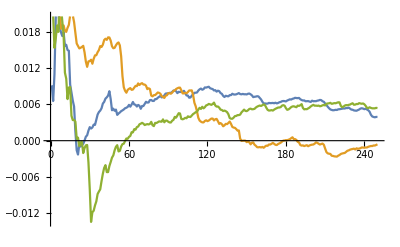

```mathematica
ListLinePlot[Gsteps4096]
```

```mathematica
GNomalize=Table[Table[Gsteps[[i,N]]/Gsteps[[i,250]],{N,250}],{i,8}];
```

```mathematica
area=data[[1,1,4]]*data[[1,1,1]];
```

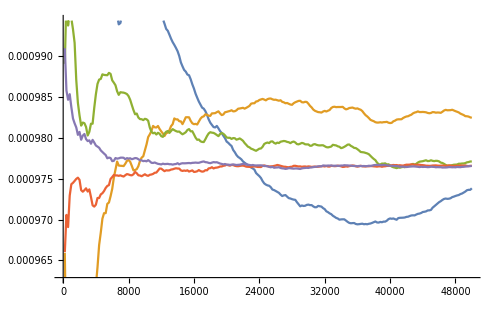

```mathematica
samplesize=Table[200 i,{i,250}];
ListLinePlot[Table[Table[{N,1/area Mean[insGs1024[[i]][[1;;N]]]/Mean[insGs1024[[i]]]},{N,samplesize}],{i,5}]]
```

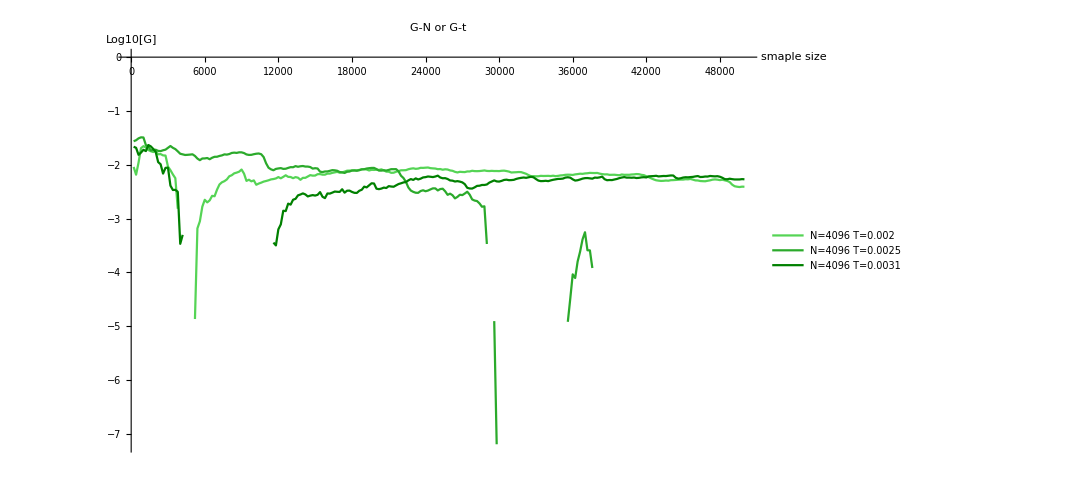

```mathematica
LowT4096=ListLinePlot[Table[Table[{samplesize[[n]],Log10[Gsteps4096[[i,n]]]},{n,250}],{i,3}],PlotStyle->Table[Blend[{GrayLevel[1-i/3],RGBColor[0,1,0]},0.5],{i,3}],PlotLegends->Table[StringJoin["N=4096 T=",ToString[Tlist4096[[i]]]],{i,3}],AxesLabel->{"smaple size","Log10[G]"},ImageSize->800,PlotLabel->"G-N or G-t",PlotRange->All]
```

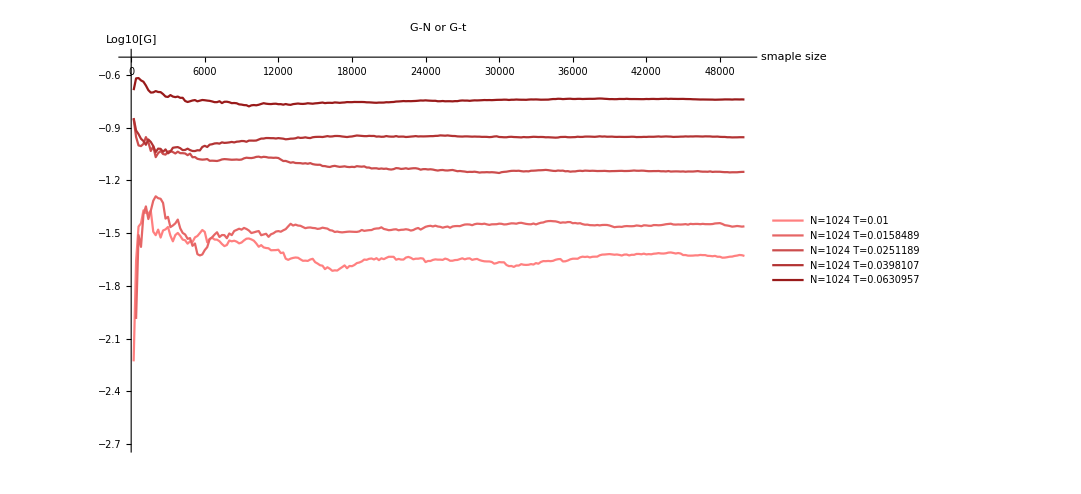

```mathematica
HighT=ListLinePlot[Table[Table[{samplesize[[n]],Log10[Gsteps[[i,n]]]},{n,250}],{i,4,8}],PlotStyle->Table[Blend[{GrayLevel[1-i/5],RGBColor[1,0,0]},0.5],{i,0,5}],PlotLegends->Table[StringJoin["N=1024 T=",ToString[Tlist1024[[i+3]]]],{i,5}],AxesLabel->{"smaple size","Log10[G]"},ImageSize->800,PlotLabel->"G-N or G-t",PlotRange->{Automatic,{-0.5,-2.7}}]
```

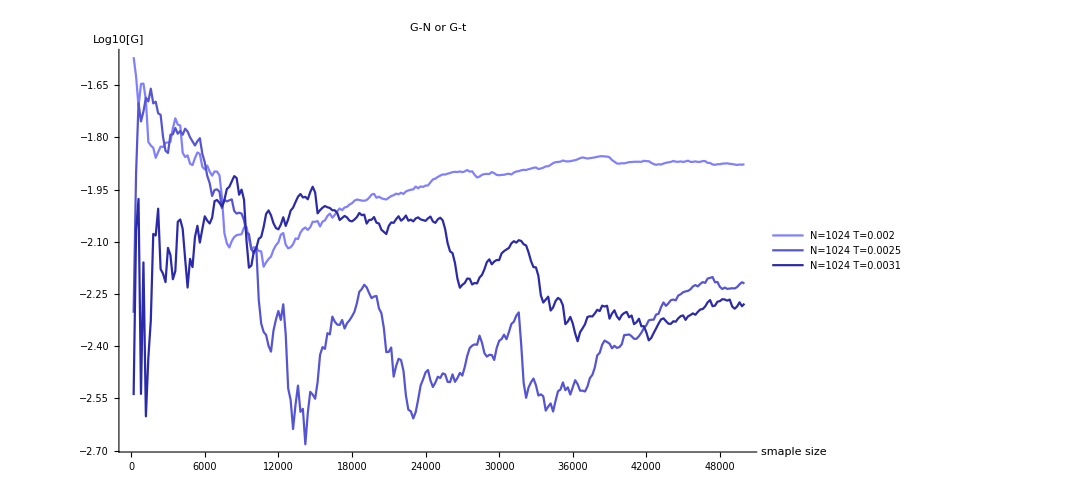

```mathematica
LowT=ListLinePlot[Table[Table[{samplesize[[n]],Log10[Gsteps[[i,n]]]},{n,250}],{i,3}],PlotStyle->Table[Blend[{GrayLevel[1-i/3],RGBColor[0,0,1]},0.5],{i,0,3}],PlotLegends->Table[StringJoin["N=1024 T=",ToString[Tlist1024[[i]]]],{i,8}],AxesLabel->{"smaple size","Log10[G]"},ImageSize->800,PlotLabel->"G-N or G-t"]
```

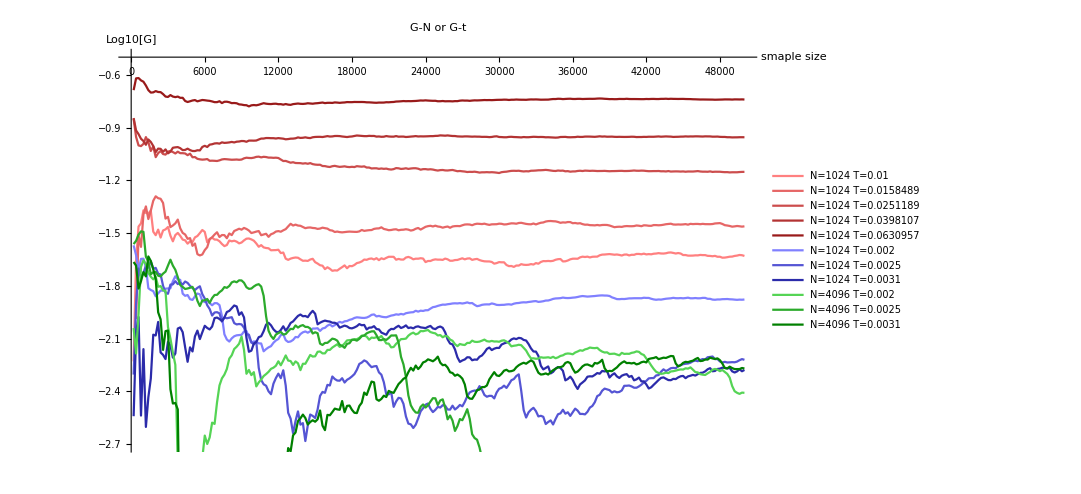

```mathematica
Show[HighT,LowT,LowT4096]
```

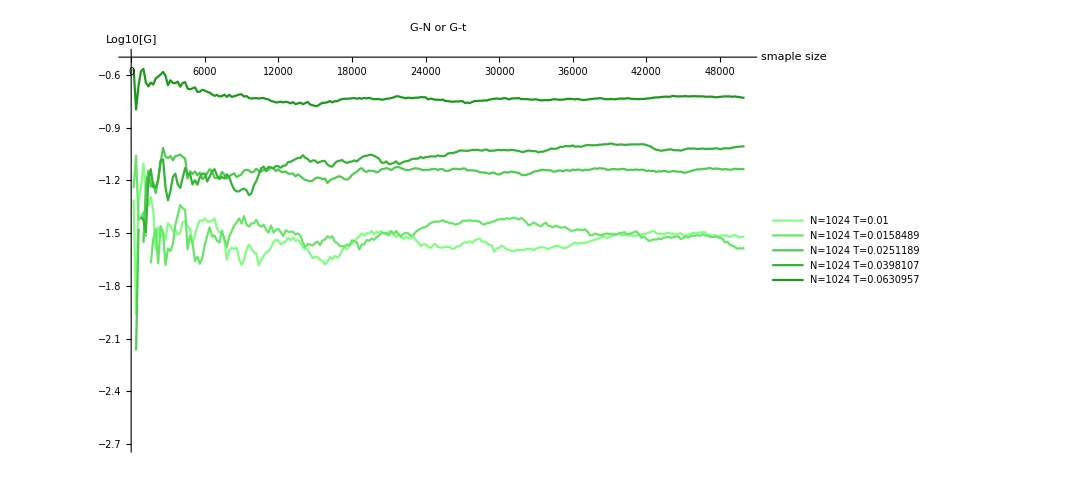

```mathematica
HighTSpacing10=ListLinePlot[Table[Table[{samplesize[[n]],Log10[GstepsSpacing10[[i,n]]]},{n,250}],{i,4,8}],PlotStyle->Table[Blend[{GrayLevel[1-i/5],RGBColor[0,1,0]},0.5],{i,0,5}],PlotLegends->Table[StringJoin["N=1024 T=",ToString[Tlist1024[[i+3]]]],{i,5}],AxesLabel->{"smaple size","Log10[G]"},ImageSize->800,PlotLabel->"G-N or G-t",PlotRange->{Automatic,{-0.5,-2.7}}]
```

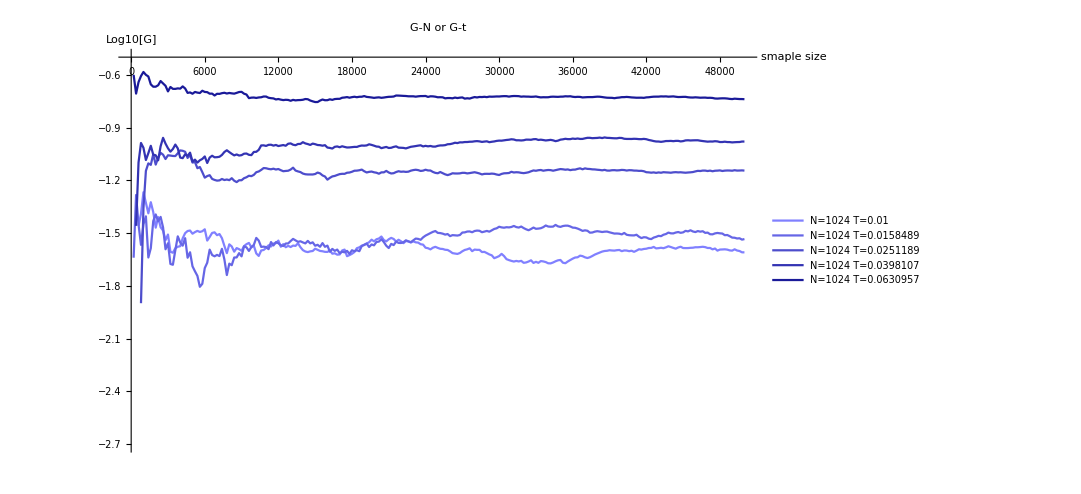

```mathematica
HighTSpacing5=ListLinePlot[Table[Table[{samplesize[[n]],Log10[GstepsSpacing5[[i,n]]]},{n,250}],{i,4,8}],PlotStyle->Table[Blend[{GrayLevel[1-i/5],RGBColor[0,0,1]},0.5],{i,0,5}],PlotLegends->Table[StringJoin["N=1024 T=",ToString[Tlist1024[[i+3]]]],{i,5}],AxesLabel->{"smaple size","Log10[G]"},ImageSize->800,PlotLabel->"G-N or G-t",PlotRange->{Automatic,{-0.5,-2.7}}]
```

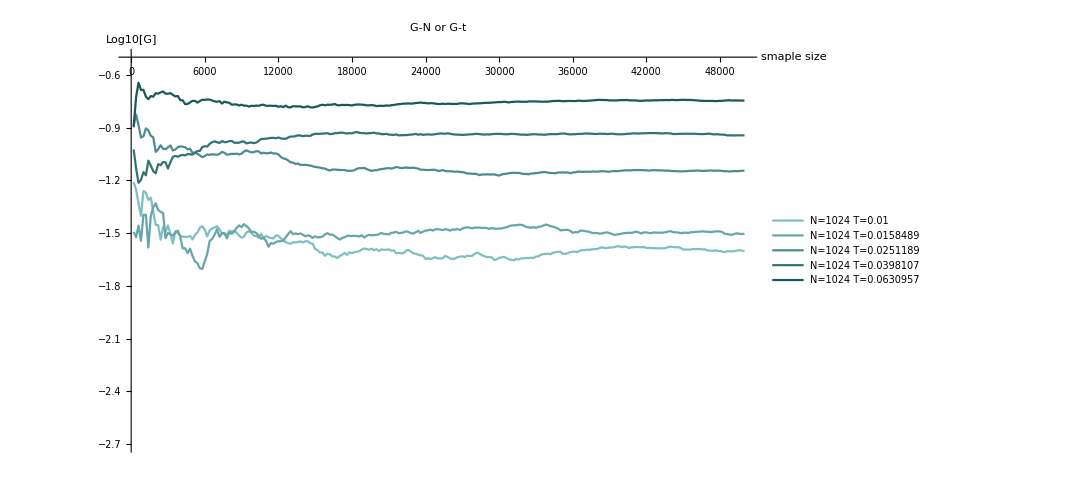

```mathematica
HighTSpacing2=ListLinePlot[Table[Table[{samplesize[[n]],Log10[GstepsSpacing2[[i,n]]]},{n,250}],{i,4,8}],PlotStyle->Table[Blend[{GrayLevel[1-i/5],RGBColor[0,0.5,0.5]},0.5],{i,0,5}],PlotLegends->Table[StringJoin["N=1024 T=",ToString[Tlist1024[[i+3]]]],{i,5}],AxesLabel->{"smaple size","Log10[G]"},ImageSize->800,PlotLabel->"G-N or G-t",PlotRange->{Automatic,{-0.5,-2.7}}]
```

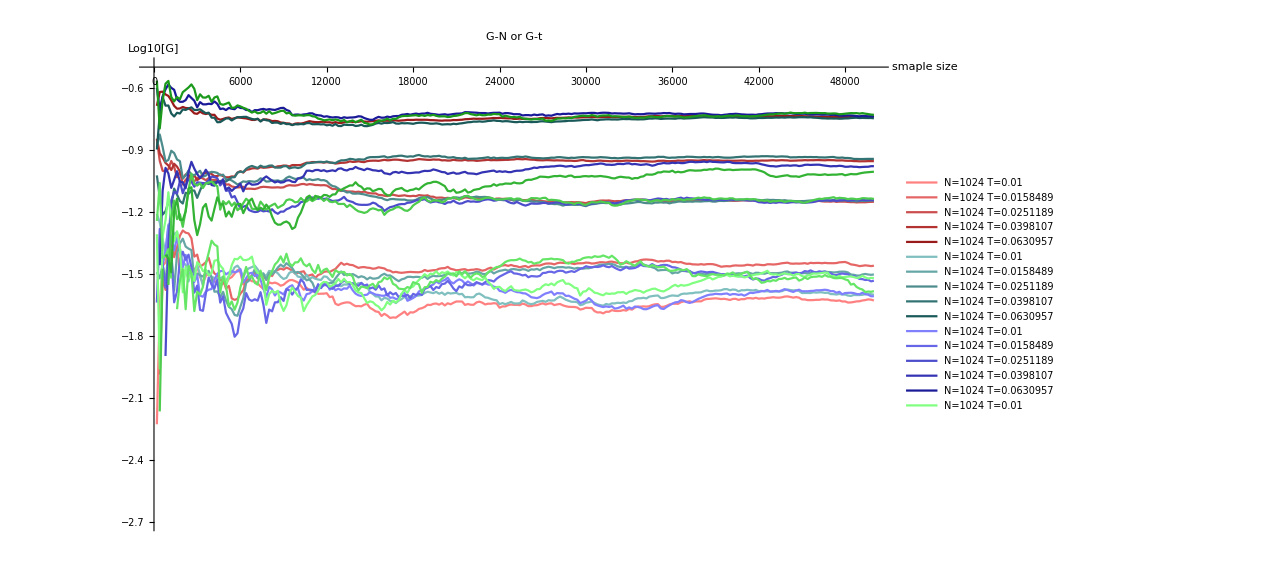

```mathematica
Show[HighT,HighTSpacing2,HighTSpacing5,HighTSpacing10]
```

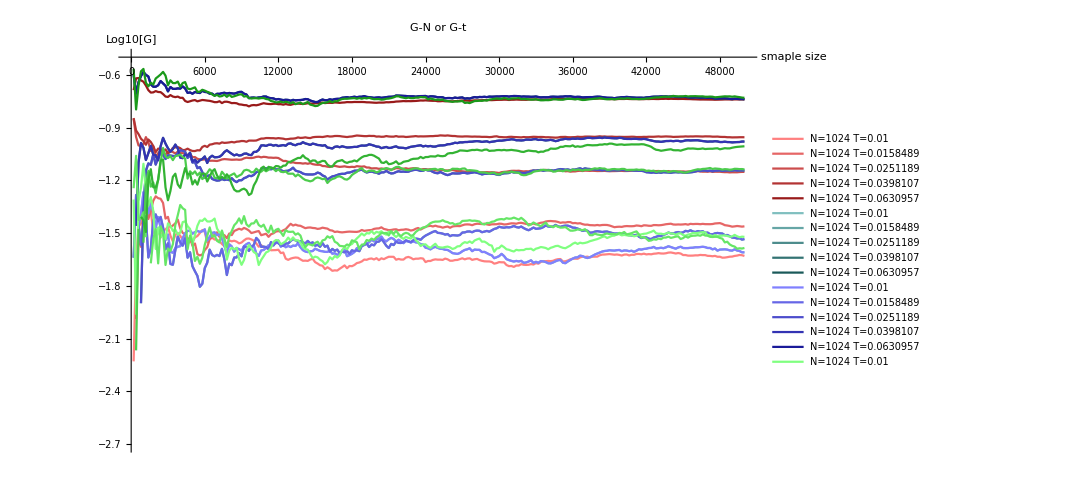

```mathematica
Show[HighT,HighTSpacing2,HighTSpacing5,HighTSpacing10]
```

```mathematica
Gsteps[[1;;2]][[1]]
```

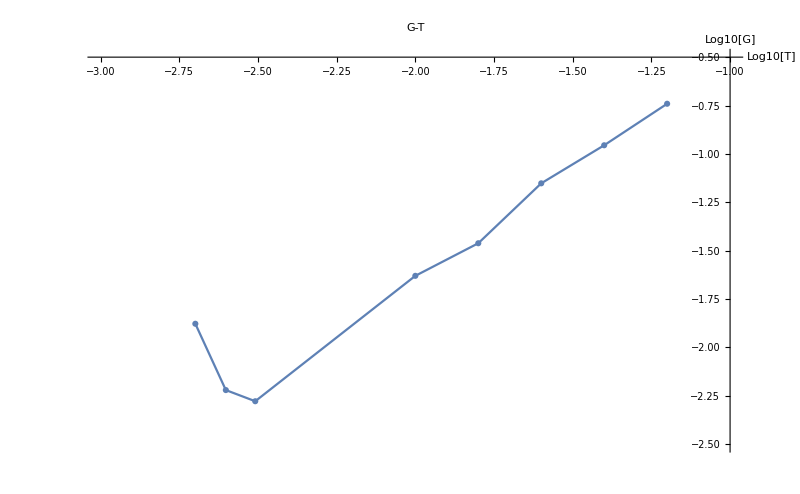

```mathematica
ListLinePlot[Table[{Log10[Tlist1024[[i]]],Log10[Gsteps[[i,250]]]},{i,8}],PlotMarkers->Automatic,AxesLabel->{"Log10[T]","Log10[G]"},ImageSize->800,PlotLabel->"G-T",PlotRange->{{-3,-1},{-2.5,-0.5}}]
```

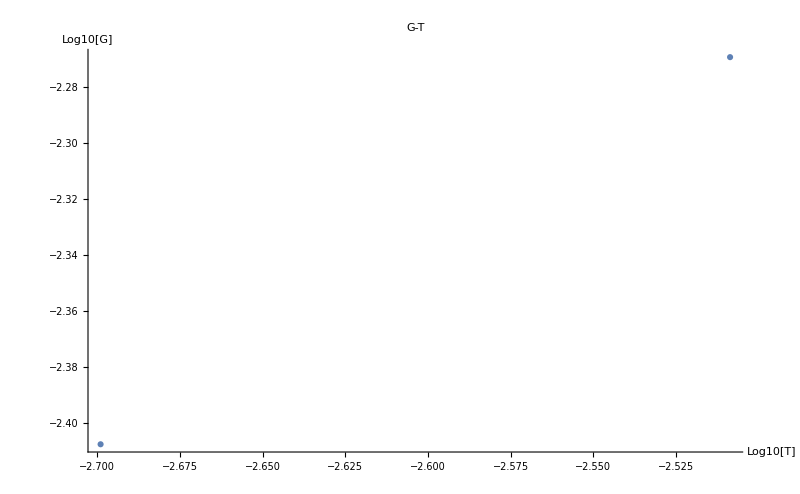

```mathematica
ListLinePlot[Table[{Log10[Tlist4096[[i]]],Log10[Gsteps4096[[i,250]]]},{i,3}],PlotMarkers->Automatic,AxesLabel->{"Log10[T]","Log10[G]"},ImageSize->800,PlotLabel->"G-T"]
```

```mathematica
Table[{Log10[Tlist1024[i]],Log10[Gsteps[[i,250]]]},{i,2}]
```

{{Log[{0.002,0.0025,0.0031,0.01,0.0158489,0.0251189,0.0398107,0.0630957}[1]]/Log[10],-1.87739},{Log[{0.002,0.0025,0.0031,0.01,0.0158489,0.0251189,0.0398107,0.0630957}[2]]/Log[10],-2.22004}}

```mathematica
Length[sisf[[1]]]
```

35

```mathematica
timeNVT[[35]]
```

63095.7

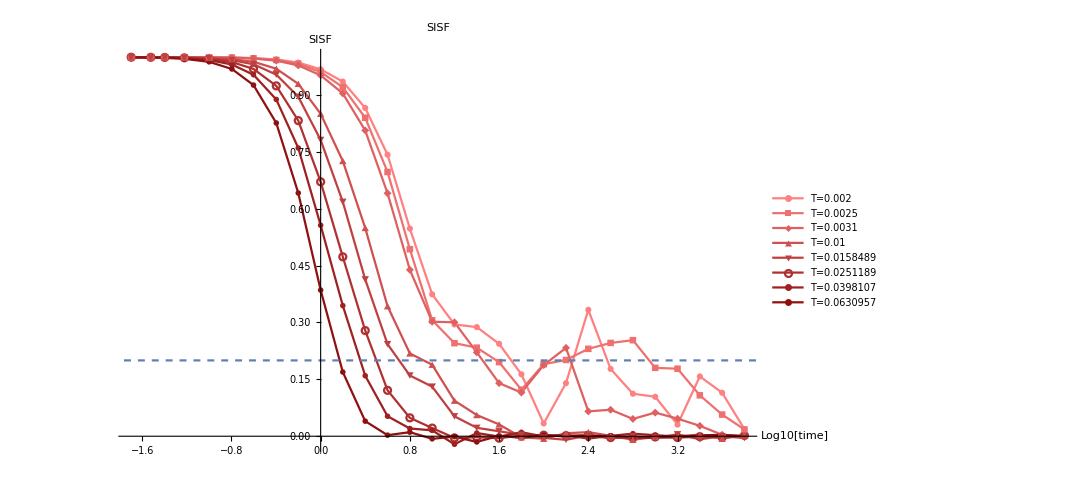

```mathematica
SISFPLOT=ListLinePlot[Table[Table[{Log10[timeNVT[[time]]],sisf[[i,time]]},{time,30}],{i,8}],PlotLegends->Table[StringJoin["T=",ToString[Tlist1024[[i]]]],{i,8}],AxesLabel->{"Log10[time]","SISF"},PlotStyle->Table[Blend[{GrayLevel[1-i/8],RGBColor[1,0,0]},0.5],{i,0,8}],PlotMarkers->Automatic,ImageSize->800,PlotLabel->"SISF"];
tau=Plot[0.2,{x,-10,100},PlotStyle->Dashed];
Show[SISFPLOT,tau]
```

```mathematica
10^0.2
```

1.58489